# MCF Exercises

#### Funzioni in campo complesso

```mathematica
z=2+3 I
```

2+3 ⅈ

```mathematica
FullForm[z]
```

Complex[2,3]

```mathematica
Log[z]
```

Log[2+3 ⅈ]

```mathematica
N[Log[z]]
```

1.28247+0.982794 ⅈ

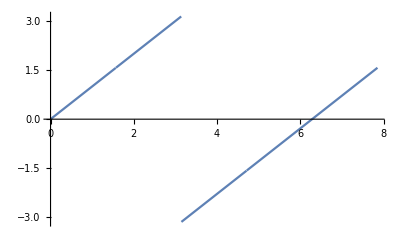

```mathematica
Plot[Log[E^(I t)]/I,{t,0,5/2 Pi}]
```

```mathematica
Log[-1-0.0001I]
```

5.×10^-9-3.14149 ⅈ

```mathematica
Normal[Series[Log[1+x],{x,0,30}]]/.x->-0.9
```

-2.29263

```mathematica
Log[0.1]
```

-2.30259

```mathematica
Solve[0.9^n/n==0.001,n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→32.5169}}

```mathematica
Log[0.001]/Log[0.9]-1
```

64.563

```mathematica
For
```

```mathematica
r[x_,y_]:=Power[x,y]
```

```mathematica
r[2,3]
```

8

```mathematica
r[3,2]
```

8

```mathematica
SetAttributes[r,Orderless]
```

```mathematica
r[2,-1]
```

1

```mathematica
Coefficient[e^(x^2),e,x^2]
```

1

## Esercizio: Implementa una funzione myCoefficient

```mathematica
??Coefficient
```

```mathematica
??Collect
```

```mathematica
myCoefficient[expr_,form_]:=Module[{temp,res},
temp=Expand[expr];
Which[
Head[temp]===Plus,
res=Map[monomialCoefficient[#,form]&,temp],
True,
res=monomialCoefficient[expr,form]
];
Return[res];
]
```

```mathematica
monomialCoefficient::number="Argument `1` not valid"
```

Argument `1` not valid

```mathematica
monomialCoefficient[expr_,form_]:=Module[{temp,res, coeff},
If[NumberQ[form],
Message[monomialCoefficient::number,form];
Return[$Failed]
];
If[MatchQ[expr,c_. form],
coeff=expr/.{c_. form->c};
]
Which[
MatchQ[expr,c_. form],
res=coeff,
True,
res=0
];
Return[res];
];
```

### Test di Coefficient

```mathematica
Coefficient[E^Cos[x] Cos[x],Cos[x]]
```

ⅇ^Cos[x]

```mathematica
myCoefficient[2 a ^x x+ 3x,r]
```

0

```mathematica
monomialCoefficient[x^2 2 ,2]
```

monomialCoefficient::number: Argument 2 not valid

$Failed

```mathematica
(!NumberQ[2])
```

False

```mathematica
??NumberQ
```

```mathematica
Coefficient[2 x, 2.]
```

Coefficient::ivar: 2. is not a valid variable.

Coefficient[2 x,2.]

```mathematica
??MatchQ
```